### Naloga 1

```mathematica
GG=9.81;
H=10;
v0={10, 3};
x0={0, H};
a0={0, -GG};
X[t_]:=x0+v0 t+a0 t^2/2
```

```mathematica
X[t]
```

```mathematica
{10 t,10+3 t-4.905 t^2}
```

```mathematica
SlikaTocke[t_]:={PointSize[0.03], Point[X[t]]}
```

```mathematica
Graphics@SlikaTocke[1]
```

-Graphics-

```mathematica
SlikaTocke[1]
```

Point[{10,8.095}]

```mathematica
V[t_]:=D[X[tt], tt]/.tt->t
```

```mathematica
V[1]
```

{10,-6.81}

```mathematica
V[t_]:=v0 +a0 t
V[t]
```

{10,3-9.81 t}

```mathematica
SlikaVektorja[t_,k_]:={Thickness[0.005], Arrow[{X[t], X[t] + V[t]*k}]}
```

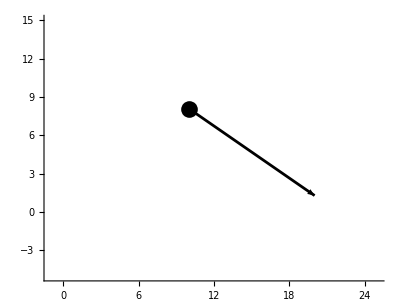

```mathematica
Graphics[{SlikaVektorja[1, 1], SlikaTocke[1]}, PlotRange-> {{-1, 25},{-5, 15}}, Axes->True, AspectRatio->Automatic]
```

```mathematica
?*Size
```

```mathematica
Slika[t_]:=Graphics[{SlikaVektorja[t,1], SlikaTocke[t]}, PlotRange-> {{-1, 25},{-5, 15}}, Axes->True, AspectRatio->Automatic]
```

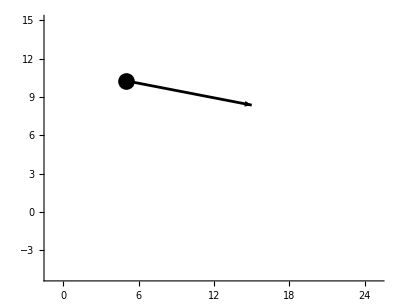

```mathematica
Slika[0.5]
```

```mathematica
Manipulate[Slika[t], {t, 0,5}]
```

```mathematica
?Slika
```

```mathematica
ClearAll[Slika]
```

```mathematica
casPristanka=t/.Solve[X[t][[2]]==0&&t>0, t]//First
```

1.76604

```mathematica
dolzinaPristanka=X[casPristanka]//First
```

17.6604

```mathematica
casMaxVisine=t/.Solve[D[X[t][[2]], t]==0, t]//First
```

0.30581

```mathematica
maxVisina=X[casMaxVisine][[2]]
```

10.4587

```mathematica
ClearAll[Slika]
```

```mathematica
Slika[t_]:=Graphics[{SlikaVektorja[t,0.5], SlikaTocke[t]}, PlotRange-> {{-1, dolzinaPristanka+5},{-5, maxVisina+1}}, Axes->True, AspectRatio->Automatic]
```

```mathematica
Manipulate[Slika[t], {t, 0,casPristanka}]
```

```mathematica
V[casPristanka]//Norm
```

17.47

```mathematica
V[casMaxVisine]
```

{10.,0.}

### Naloga 2

```mathematica
r111=Ravnina[{-1,-1,-1},{1,1,1}]
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
Slika[Ravnina[n_, v_]]:=Hyperplane[n, v]
```

```mathematica
Slika[r111]
```

Hyperplane[{-1,-1,-1},{1,1,1}]

```mathematica
Graphics3D[Slika[r111]]
```

-Graphics3D-

```mathematica
Normala[Ravnina[n_, v_]]:=n
```

```mathematica
Tocka[Ravnina[n_, v_]]:=v
```

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}]
```

Ravnina[{1,0,0},{0,0,0}]

```mathematica
ry=Ravnina[{0, 1, 0}, {0, 0, 0}]
```

Ravnina[{0,1,0},{0,0,0}]

```mathematica
rz=Ravnina[{0, 0, 1}, {0, 0, 0}]
```

Ravnina[{0,0,1},{0,0,0}]

```mathematica
Graphics3D@Map[Slika,{r111, rx, ry, rz}]
```

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_, v_]]:=Arrow[{v, v+n}]
```

```mathematica
SlikaNormale[r111]
```

Arrow[{{1,1,1},{0,0,0}}]

```mathematica
Graphics3D[{Slika[r111], SlikaNormale[r111]}, PlotRange-> {{-2,2},{-2,2},{-2,2}}, Axes->True, AxesOrigin->{0, 0, 0}]
```

-Graphics3D-

```mathematica
Enacba[Ravnina[n_, v_]]:=n.({x, y, z}-v)==0
```

```mathematica
Enacba[rx]
```

x==0

```mathematica
ResiSistem[sistem_List]:= Solve [sistem, {x, y, z}]
```

```mathematica
Ravnina[r111, rx, ry, rz]
```

Ravnina[Ravnina[{-1,-1,-1},{1,1,1}],Ravnina[{1,0,0},{0,0,0}],Ravnina[{0,1,0},{0,0,0}],Ravnina[{0,0,1},{0,0,0}]]

```mathematica
ravnine{r111, rx, ry, rz}
```

```mathematica
resitveDvojno={x, y, z}/. Map[ResiSistem,Subsets[Map[Enacba, {r111, rx, ry, rz}], {3}]]
```

{{{0,0,3}},{{0,3,0}},{{3,0,0}},{{0,0,0}}}

```mathematica
tocke=Map[First, resitveDvojno]
```

{{0,0,3},{0,3,0},{3,0,0},{0,0,0}}

```mathematica
Presecisca[ravnine_List]:= Module[{resitveDvojno},
resitveDvojno={x, y, z}/. Map[ResiSistem,Subsets[Map[Enacba, {r111, rx, ry, rz}], {3}]];
Map[First, resitveDvojno]
]
```